```mathematica
(*碰撞变轨*)
```

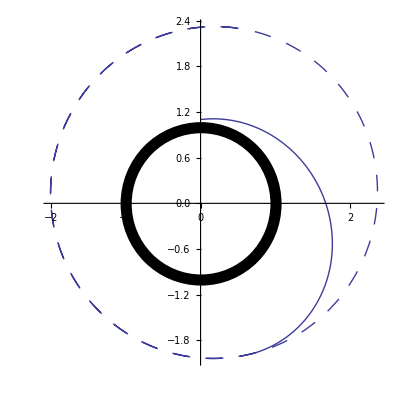

```mathematica
tm1=1;P=4.0 π^2;
xinitial1={0,6.8};yinitial1={1.1,0.8};
(*orbit before colliding*)
eqs1={x''[t]==-P*x[t]/((x[t]^2+y[t]^2)^(3/2)),
y''[t]==-P*y[t]/((x[t]^2+y[t]^2)^(3/2)),
x[0]==xinitial1[[1]],x'[0]==xinitial1[[2]],
y[0]==yinitial1[[1]],y'[0]==yinitial1[[2]]};
s=NDSolve[eqs1,{x,y},{t,0,tm1}];
{x,y}={x,y}/.s[[1]];
g1=ParametricPlot[{x[t],y[t]},{t,0,tm1},Epilog->{Thickness[0.02],Circle[{0,0},1]}];
(*orbit after colliding*)
tm2=5;
xinitial2={x[tm1],x'[tm1]*1.25};yinitial2={y[tm1],1.1*y'[tm1]};
Clear[x,y]
eqs2={x''[t]==-P*x[t]/((x[t]^2+y[t]^2)^(3/2)),
y''[t]==-P*y[t]/((x[t]^2+y[t]^2)^(3/2)),
x[0]==xinitial2[[1]],x'[0]==xinitial2[[2]],
y[0]==yinitial2[[1]],y'[0]==yinitial2[[2]]};
s=NDSolve[eqs2,{x,y},{t,0,tm2}];
{x,y}={x,y}/.s[[1]];
g2=ParametricPlot[{x[t],y[t]},{t,0,tm2},PlotStyle->{Dashing[{0.03,0.03}]}];
Show[{g1,g2},PlotRange->All]
```

```mathematica
Clear[tm1,tm2,x,y,g1,g2,s,xinitial1,xinitial2,yinitial1,yinitial2,eqs1,eqs2,P]
```

```mathematica
(*非球对称引力场导致的变轨*)
```

```mathematica
θ=80*π/180;
tm=100;P=4.0 π^2;
xinitial={0,6.5};
yinitial={1.1Cos[θ],0.8};
zinitial={1.1Sin[θ],0.5};
p0={0,0,0};
p={xinitial[[1]],yinitial[[1]],zinitial[[1]]};
ξ=10^-2;r=√(x[t]^2+y[t]^2+z[t]^2);
eqs={x''[t]==-P/r^3((2ξ*z[t])/r+1)x[t],y''[t]==-P/r^3((2ξ*z[t])/r+1)y[t],z''[t]==-P/r^3(((2ξ*z[t])/r+1)z[t]-ξ*r),
x[0]==xinitial[[1]],x'[0]==xinitial[[2]],
y[0]==yinitial[[1]],y'[0]==yinitial[[2]],
z[0]==zinitial[[1]],z'[0]==zinitial[[2]]};
s=NDSolve[eqs,{x,y,z},{t,0,tm},MaxSteps->∞];
{x,y,z}={x,y,z}/.s[[1]];
g1=ParametricPlot3D[{x[t],y[t],z[t]},{t,0,tm},PlotPoints->5000,AxesLabel->{"x","y","z"}];
g2=Graphics3D[{PointSize[0.05],Point[p0],Point[p]}];
Show[g1,g2]
```

-Graphics3D-

```mathematica
Clear[θ,tm,xinitial,yinitial,zinitial,p0,p,x,y,z,s,eqs,ξ,P,g1,g2,r]
```

```mathematica
|
```